```mathematica
diffeq=x'[t]==r x[t](1-x[t]/k)
```

x'[t]==r x[t] (1-x[t]/k)

```mathematica
Needs["MaTeX`"]
```

```mathematica
TeXify[x_,n_]:=MaTeX[x,FontSize->n]//Quiet
```

#### Print version

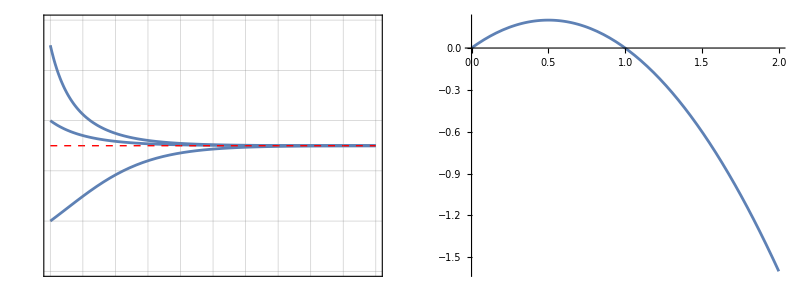

/Users/emasroo1/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Logistic Equation/logistic.pdf

```mathematica
With[{tfinal=10,rval=0.8,kval=1,initialvalue=1.8},With[{sol=NDSolve[{diffeq/.{r->rval,k->kval},x[0]=={1.8,1.2,0.4}},x[t],{t,0,tfinal}]},
GraphicsRow@{Plot[x[t]/.sol,{t,0,tfinal},
PlotRange->{{0,10},{0,2}},
Frame->True,
FrameLabel->{TeXify["\\text{Time }(t)",16],TeXify["\\text{Population }N(t)",16]},
FrameTicks->{{With[{vals=Table[ 0.4i,{i,0,5}]},Transpose[{vals,TeXify[#,14]&/@vals}]],None},{With[{vals=Table[i,{i,0,tfinal}]},Transpose[{vals,TeXify[#,14]&/@vals}]],None}},
GridLines->Automatic,Epilog->{Directive[Red,Dashed],Line[{{0,kval},{tfinal,kval}}]}
],Plot[rval x(1-x/kval),{x,0,2kval},
PlotRange->{All,All},AxesLabel->{TeXify["N",16],TeXify["\\dot{N}",16]}]
}
]]
Export[NotebookDirectory[]<>"logistic.pdf",%]
```

#### Web version

```mathematica
With[{tfinal=10},Manipulate[With[{sol=NDSolve[{diffeq/.{r->rval,k->kval},x[0]==initialvalue},x[t],{t,0,tfinal}]},
GraphicsRow@{Plot[x[t]/.sol,{t,0,tfinal},
PlotRange->{{0,10},{0,2}},
Frame->True,
FrameLabel->{"Time (t)","Population N(t)"},
GridLines->Automatic,Epilog->{Directive[Red,Dashed],Line[{{0,kval},{tfinal,kval}}]}
],Plot[rval x(1-x/kval),{x,0,2kval},
PlotRange->{All,{-rval,rval}},AxesLabel->{"N","Ṅ"}]
}
],{rval,0.1,5},{kval,0.4,2},{initialvalue,0,2.4}]]
```

#### Deploy

```mathematica
(*CloudDeploy[%71,Permissions->"Public"]*)
```